## 《数学实验》课程简介

利用数学工具学习数学知识、研究数学问题的过程，称为数学实验。

通过实验加深对课本知识的理解和运用。

通过实验培养发现问题和解决问题的能力。

围绕问题开展实验，观察现象，提出问题，尽力解决。

教学形式：课堂教学+课后上机实践。

总评成绩：4次平时作业+课堂表现。

平时作业：选取一个数学问题展开研究。形式为实验报告小论文。

鼓励自选研究问题，并作课堂展示。

如有抄袭作假，以考试作弊论。

## 实验一、基础数学实验

### 例1：平面代数曲线 f(x,y)=0的性质，其中 f 是多项式。

```mathematica
Manipulate[ContourPlot[x^3+y^3==a x y,{x,-5,5},{y,-5,5}],{a,-5,5}]
```

思考：上述曲线有渐近线？渐近线方程？如何求交叉点？

思考：对于哪些 f (x,y) ，曲线 f(x,y)=0有自交现象？

```mathematica
Manipulate[ContourPlot[x^3+y^3==1+a x y,{x,-5,5},{y,-5,5}],{a,-5,5}]
```

思考：对于哪些 f (x,y) ，曲线 f(x,y)=0有多个分支？有几个？

### 例2：平面参数曲线 {x=f(t) y=g(t)的性质，其中 f,g 是正余弦函数。

{-0.934753 Cos[t]+0.856786 Cos[2 t],-0.754404 Sin[t]-0.660319 Sin[2 t]}

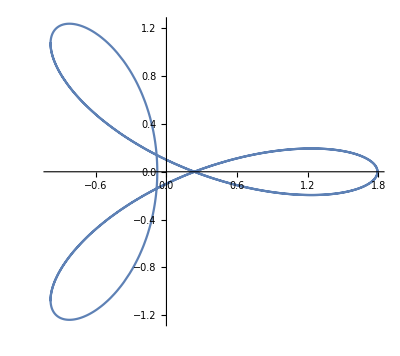

```mathematica
Clear[x,y,t];{x=RandomReal[{-1,1},2].{Cos[t],Cos[2t]},y=RandomReal[{-1,1},2].{Sin[t],Sin[2t]}}
ParametricPlot[{x,y},{t,-5,5}]
```

思考：对于上述类型的参数曲线，有哪些结论？

### 例3：射影变换的性质。

商空间 R^3/～ 称为射影平面，其中 α~β⇔α=λβ(λ是非零实数)。
映射 [α]↦[A α]称为射影变换，其中 A 是 R^3 上线性变换。

```mathematica
{a1,a2,a3,a4,a5,a6,a7,a8,a9}=RandomReal[{-1,1},9];
f[{x_,y_}]:={(a1 x+a2 y+a3)/(a7 x+a8 y+a9),(a4 x+a5 y+a6)/(a7 x+a8 y+a9)};
```

```mathematica
Manipulate[Show[
ParametricPlot[f[{d,y}],{y,-d,d}],
ParametricPlot[f[{x,d}],{x,-d,d}],
ParametricPlot[f[{-d,y}],{y,-d,d}],
ParametricPlot[f[{x,-d}],{x,-d,d}],PlotRange->All
],{d,0.001,1}]
```

思考：射影变换是否总是把直线变成直线？

```mathematica
Manipulate[ParametricPlot[f[r{Cos[t],Sin[t]}],{t,0,2 π}],{r,0.001,1}]
```

思考：射影变换是否总是把圆锥曲线变成圆锥曲线？

### 例4：复平面上的分式线性变换。

```mathematica
Clear[f,p];f[z_]:=1/z;p[z_]:={Re[z],Im[z]};
```

-0.949751-0.392805 ⅈ

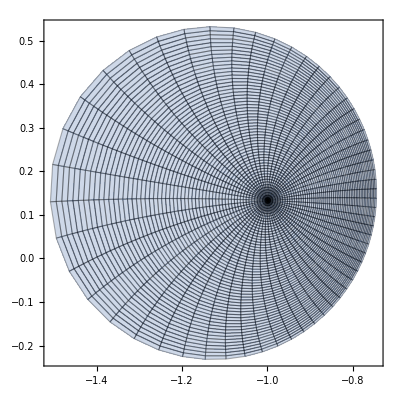

```mathematica
c=RandomComplex[{-1-I,1+I}]
ParametricPlot[p@f[r ⅇ^(ⅈ t)+c],{r,0,1},{t,0,2 π},Mesh->All,PlotRange->All]
```

-0.790571+0.641758 ⅈ

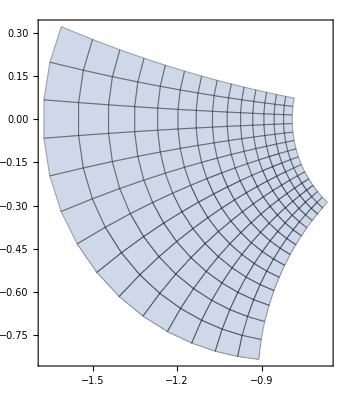

```mathematica
c=RandomComplex[{-1-I,1+I}]
ParametricPlot[p@f[(x+I y)+c],{x,-1,1},{y,-1,1},Mesh->All,PlotRange->All]
```

思考：视直线为半径∞的圆。分式线性变换是否总是把圆变成圆？

思考：(圆(x-a))^2+(y-b)^2=r^2 的像的方程？直线 y=k x+c 的像的方程？

思考：分式线性变换与射影变换的关系。

### 例5：复解析函数在零点、极点、奇点附近的性质。

```mathematica
Clear[p];p[z_]:={Re[z],Im[z]};
```

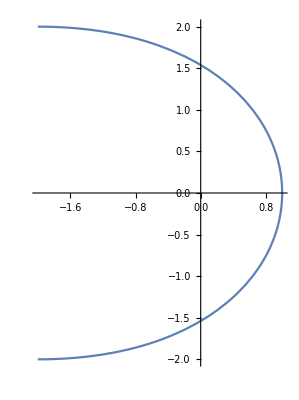
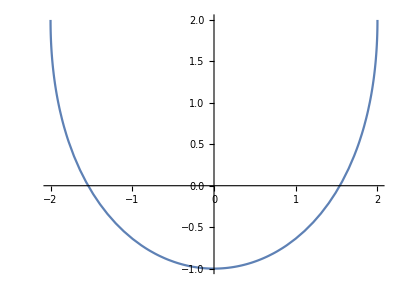
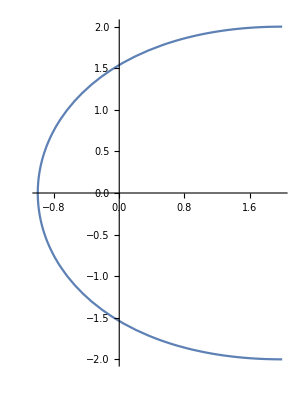
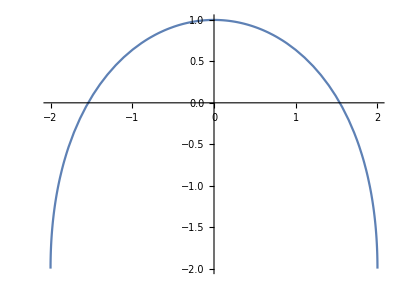

```mathematica
Clear[f];f[z_]:=z^3;d=1;
{ParametricPlot[p@f[d+ⅈ y],{y,-d,d},PlotRange->All],
ParametricPlot[p@f[x+ⅈ d],{x,-d,d},PlotRange->All],
ParametricPlot[p@f[-d+ⅈ y],{y,-d,d},PlotRange->All],
ParametricPlot[p@f[x-ⅈ d],{x,-d,d},PlotRange->All]
}
```

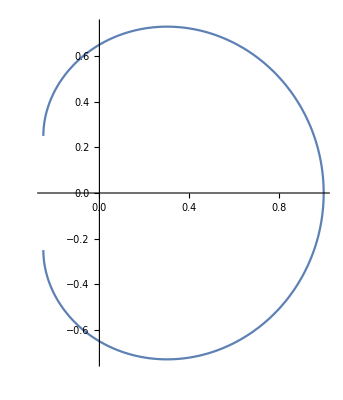
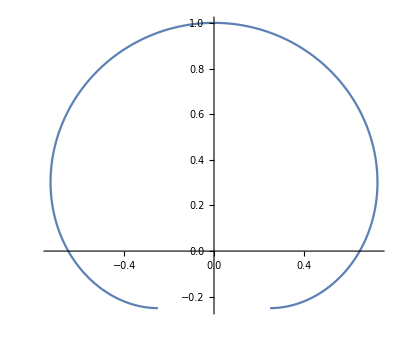
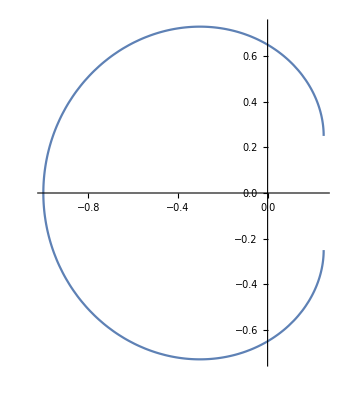
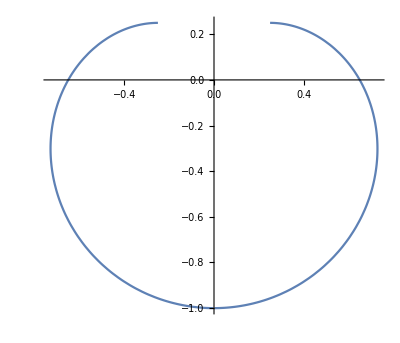

```mathematica
Clear[f];f[z_]:=z^-3;d=1;
{ParametricPlot[p@f[d+ⅈ y],{y,-d,d},PlotRange->All],
ParametricPlot[p@f[x+ⅈ d],{x,-d,d},PlotRange->All],
ParametricPlot[p@f[-d+ⅈ y],{y,-d,d},PlotRange->All],
ParametricPlot[p@f[x-ⅈ d],{x,-d,d},PlotRange->All]}
```

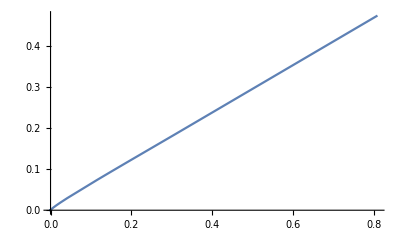
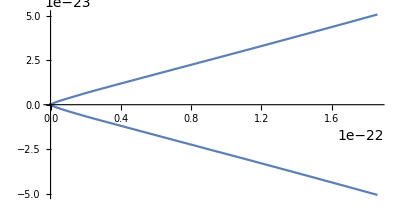
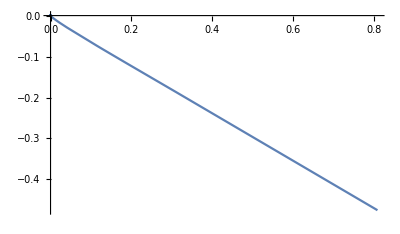
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Clear[f];f[z_]:=Exp[1/z];d=0.01;
{ParametricPlot[p@f[d+ⅈ y],{y,-d,d},PlotRange->All],
ParametricPlot[p@f[x+ⅈ d],{x,-d,d},PlotRange->All],
ParametricPlot[p@f[-d+ⅈ y],{y,-d,d},PlotRange->All],
ParametricPlot[p@f[x-ⅈ d],{x,-d,d},PlotRange->All]}
```

### 例6：围道积分与零点、极点个数。

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.1269×10^-7}. NIntegrate obtained 1.04083×10^-16-4.77049×10^-18 ⅈ and 1.59575×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 9.54098×10^-17-2.34188×10^-17 ⅈ and 3.88327×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.1269×10^-7}. NIntegrate obtained 3.29597×10^-16-1.46801×10^-16 ⅈ and 8.25852×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0,0,0,0,0,0,1,1,4,5,6,8,9,9,9,9,10,10,10,10}

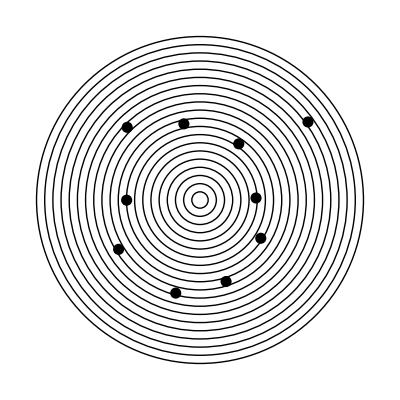

```mathematica
n=10;c=RandomComplex[{-1-I,1+I},n+1];Clear[f,z];f[z_]:=c.Table[z^i,{i,0,n}];w=z/.NSolve[f[z]==0,z];
Table[Round[1/(2 π)NIntegrate[f'[r ⅇ^(ⅈ t)]/f[r ⅇ^(ⅈ t)] r ⅇ^(ⅈ t),{t,0,2Pi}]],{r,0.1,2,0.1}]
Graphics[{Table[Circle[{0,0},r],{r,0.1,2,0.1}],PointSize[0.02],Point[p/@w]}]
```

思考：把平面分成方格，对每个方格作围道积分，搜索其中的零点位置。

### 例7：辗转相除法与连分数。

```mathematica
ExtendedEuclid[m_Integer,n_Integer]:=Module[{a,b,c,t},
a=m;b=n;c={};
While[b≠0,t=Floor[a/b];{a,b}={b,a-b*t};AppendTo[c,t]];
{c,a}
];
```

```mathematica
{m,n}=RandomInteger[10^10,2];{c,d}=ExtendedEuclid[m,n]
```

{{0,19,1,1,20,1,16,1,1,1,1,7,3,1,1,23},3}

由连分数求渐近分数

```mathematica
a=({{1, 0}, {0, 1}});b=Table[a=a.({{c⟦i⟧, 1}, {1, 0}});a⟦1,1⟧/a⟦2,1⟧,{i,Length[c]}]
```

{0,1/19,1/20,2/39,41/800,43/839,729/14224,772/15063,1501/29287,2273/44350,3774/73637,28691/559809,89847/1753064,118538/2312873,208385/4065937,4911393/95829424}

渐近分数的误差

{-0.0512514,0.00138017,-0.00125141,0.0000306423,-1.40896×10^-6,8.09071×10^-8,-2.88758×10^-9,1.77973×10^-9,-4.87074×10^-10,2.82821×10^-10,-2.33824×10^-11,8.76111×10^-13,-1.42861×10^-13,1.03771×10^-13,-2.5665×10^-15}

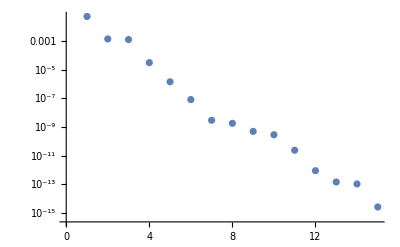

```mathematica
x=Table[N[b⟦i⟧-m/n],{i,Length[b]-1}]
ListLogPlot[Abs[x]]
```

思考：估计第 k 个渐近分数的误差与 k 的关系？

#### 辗转相除法不仅适用于两个整数，也适用于任意两个实数。

```mathematica
ExtendedEuclid[x_,y_,n_Integer]:=Module[{a,b,c,d,t},
a=x;b=y;c={};d={a};
Do[If[b==0,Break[]];t=Floor[a/b];{a,b}={b,Simplify[a-b*t]};AppendTo[c,t];AppendTo[d,a],{n}];
{c,d}
];
```

```mathematica
{c,d}=ExtendedEuclid[π,ⅇ,20]
```

{{1,6,2,2,1,2,6,8,2,1,1,1,4,3,1,1,66,2,1,1},{π,ⅇ,-ⅇ+π,7 ⅇ-6 π,-15 ⅇ+13 π,37 ⅇ-32 π,-52 ⅇ+45 π,141 ⅇ-122 π,-898 ⅇ+777 π,7325 ⅇ-6338 π,-15548 ⅇ+13453 π,22873 ⅇ-19791 π,-38421 ⅇ+33244 π,61294 ⅇ-53035 π,-283597 ⅇ+245384 π,912085 ⅇ-789187 π,-1195682 ⅇ+1034571 π,2107767 ⅇ-1823758 π,-140308304 ⅇ+121402599 π,282724375 ⅇ-244628956 π,-423032679 ⅇ+366031555 π}}

```mathematica
a=({{1, 0}, {0, 1}});b=Table[a=a.({{c⟦i⟧, 1}, {1, 0}});a⟦1,1⟧/a⟦2,1⟧,{i,Length[c]}]
```

{1,7/6,15/13,37/32,52/45,141/122,898/777,7325/6338,15548/13453,22873/19791,38421/33244,61294/53035,283597/245384,912085/789187,1195682/1034571,2107767/1823758,140308304/121402599,282724375/244628956,423032679/366031555,705757054/610660511}

```mathematica
Abs[d]//ListLogPlot
```

思考：辗转相除的余数与渐近分数的关系？估计第 k 个余数的大小？

#### 实数 x 的最佳分数近似 p/q，其中1≤q<k？

```mathematica
NearestRational[x_,k_]:=Module[{p,q,r,s,t},
r={};s=1;Do[p=Round[q*x];t=Abs[x-p/q];If[t<s,s=t;AppendTo[r,p/q]],{q,k}];r
];
```

```mathematica
NearestRational[Pi/E,1000000]
```

{1,5/4,6/5,7/6,15/13,37/32,52/45,89/77,141/122,475/411,616/533,757/655,898/777,4631/4007,5529/4784,6427/5561,7325/6338,15548/13453,22873/19791,38421/33244,61294/53035,161009/139314,222303/192349,283597/245384,628488/543803,912085/789187}

思考：最佳分数近似与渐近分数的关系？

### 例8：模变换与整系数线性方程。

求整系数线性方程组 A x=b 的整数解。

```mathematica
ModularSolve[a_,b_]:=Module[{c,d,i,j,k,m,n,p,q,r,s,t,w},
c=a;d=b;{m,n}=Dimensions[a];w=IdentityMatrix[n];
For[r=1,r≤m&&r≤n,r+=t,{p,q,t}={r,r,∞};
Do[If[0<Abs[c⟦i,j⟧]<t,{p,q,t}={i,j,Abs[c⟦i,j⟧]}],{i,r,m},{j,r,n}];
If[p≠r,c⟦{r,p}⟧=c⟦{p,r}⟧;d⟦{r,p}⟧=d⟦{p,r}⟧];
If[q≠r,c⟦All,{r,q}⟧=c⟦All,{q,r}⟧;w⟦{r,q}⟧=w⟦{q,r}⟧];
If[c⟦r,r⟧==0,Break[]];t=1;
Do[If[c⟦i,r⟧≠0,k=Round[c⟦i,r⟧/c⟦r,r⟧];
c⟦i⟧-=k c⟦r⟧;d⟦i⟧-=k d⟦r⟧;t=0],{i,r+1,m}];
Do[If[c⟦r,j⟧≠0,k=Round[c⟦r,j⟧/c⟦r,r⟧];
c⟦All,j⟧-=k c⟦All,r⟧;w⟦j⟧-=k w⟦r⟧;t=0],{j,r+1,n}]
];
r--;For[i=1,i≤r,i++,If[Mod[d⟦i⟧,c⟦i,i⟧]≠0,Print["无解"];Return[{}],d⟦i⟧/=c⟦i,i⟧]];
For[i=r+1,i≤m&&i≤n,i++,If[d⟦i⟧≠0,Print["无解"];Return[{}]]];
{d⟦1;;r⟧.w⟦1;;r⟧,w⟦r+1;;n⟧}(*{特解，基础解系}*)
];
```

```mathematica
a=({{5, 0, 0, 0, 0, 1}, {0, 715, 0, 0, 0, 1}, {0, 0, 247, 0, 0, 1}, {0, 0, 0, 391, 0, 1}, {0, 0, 0, 0, 187, 1}});b={0,10,140,245,109};ModularSolve[a,b]
```

{{-1475943123085,-10321280581,-29877391155,-18873952980,-39463719868,7379715615425},{{-1062347,-7429,-21505,-13585,-28405,5311735}}}

思考：如何求模长最小的特解？问题化为：求整数向量 x 使得|A x-b|最小。

```mathematica
{m,n}={10,8};a=RandomInteger[{-10,10},{m,n}];b=RandomInteger[{-10,10},m];MatrixForm/@{a,b}
```

{(-9 | -5 | -3 | -8 | 1 | -7 | 7 | -5
9 | 5 | 6 | 2 | 3 | 2 | 7 | -4
-6 | 8 | -1 | -7 | 8 | -10 | 3 | -4
-1 | -4 | -6 | -9 | -4 | 3 | 3 | 3
9 | -5 | 10 | 5 | -10 | -5 | 4 | -3
5 | 9 | 0 | -6 | 10 | -8 | -8 | 6
-3 | 6 | -5 | -10 | 9 | -10 | 3 | -3
9 | 1 | -9 | 3 | -8 | 3 | -5 | 9
-6 | -8 | -9 | -2 | -8 | -5 | 5 | 0
-7 | 3 | -1 | 10 | -7 | -8 | 4 | 4),(-7
-6
1
-5
-6
-5
2
10
-3
-6)}

```mathematica
x=LeastSquares[a,b];x0=Floor[x];x1=Ceiling[x];s=Tuples[Table[{x0⟦i⟧,x1⟦i⟧},{i,n}]];
k=0;r=∞;Do[t=Norm[a.s⟦i⟧-b];If[t<r,k=i;r=t],{i,Length[s]}];
{s⟦k⟧,r}
```

{{0,1,-1,0,-1,0,-2,-2},√91}

思考：上述方法是否正确？

### 例9：函数的连分式与Pade逼近。

设 f (x)=a_0+(a_1 x^r_1)/(1+(a_2 x^r_2)/(⋱+⋱/(1+(a_k x^r_k)/(1+⋯))))。[a_0,a_1 x^r_1,⋯,a_k x^r_k]称为 f(x)的前 k 项连分式。

给定 (m,n) ，设 g(x)=(p_0+p_1 x+p_m x^m)/(1+q_1 x+q_n x^n)使得 g(x)-f(x)=o(x^(m+n))。g(x)称为 f(x)的 (m,n)-Pade逼近。

```mathematica
(* f是关于x的表达式，k是正整数 *)
ContinuedFractionSeries[f_,x_Symbol,k_Integer]:=Module[{a,c,g,i},
c=f/.{x->0};a={c};g=f-c;If[g==0,Return[a]];
Do[For[i=1,(c=SeriesCoefficient[g,{x,0,i}])==0,i++];
AppendTo[a,c x^i];g=Simplify[(c x^i)/g-1];If[g==0,Break[]],{k}
];
a
];
FromContinuedFractionSeries[a_List]:=Module[{v,i},
v={0,1};Do[v=({{0, a⟦-i⟧}, {1, 1}}).v,{i,Length[a]-1}];v=({{1, a⟦1⟧}, {0, 1}}).v;Expand[v⟦1⟧]/Expand[v⟦2⟧]
];
Pade[f_,x_Symbol,m_Integer,n_Integer]:=Module[{a,b,c,i,j,k,p,q},
k=m+n+1;a=IdentityMatrix[k];b=Table[SeriesCoefficient[f,{x,0,i}],{i,0,m+n}];
Do[a⟦i,m+1+j⟧=-b⟦i-j⟧,{j,n},{i,j+1,k}];c=LinearSolve[a,b];Sum[c⟦i+1⟧ x^i,{i,0,m}]/(1+Sum[c⟦m+1+j⟧ x^j,{j,n}])
];
```

```mathematica
Clear[x];f=ArcTan[x];n=10;a=ContinuedFractionSeries[f,x,n]
g=FromContinuedFractionSeries[a]
Pade[f,x,n,n]
For[i=1,SeriesCoefficient[g-f,{x,0,i}]==0,i++];Series[g-f,{x,0,i}]
```

{0,x,x^2/3,(4 x^2)/15,(9 x^2)/35,(16 x^2)/63,(25 x^2)/99,(36 x^2)/143,(49 x^2)/195,(64 x^2)/255,(81 x^2)/323}

(x+(116 x^3)/57+(2198 x^5)/1615+(44 x^7)/133+(5597 x^9)/264537)/(1+(45 x^2)/19+(630 x^4)/323+(210 x^6)/323+(315 x^8)/4199+(63 x^10)/46189)

(x+(116 x^3)/57+(2198 x^5)/1615+(44 x^7)/133+(5597 x^9)/264537)/(1+(45 x^2)/19+(630 x^4)/323+(210 x^6)/323+(315 x^8)/4199+(63 x^10)/46189)

-(65536 x^21)/44801898141+O[x]^22

思考：f(x)的连分式展开与Pade逼近的关系。

思考：证明某些特殊函数的连分式的通项公式。

### 例10：整数方阵的行列式。

```mathematica
n=100;a=RandomInteger[{-1,1},{n,n}];Det[a]
```

47355038140718406858159418727879418399376131529306387421285445430048206

方法1：Gauss消元法

```mathematica
Det1[a_]:=Module[{c=a,d=1,g,i,j,n=Length[a],u,v},
Do[Do[If[c⟦j,i⟧==0,Continue[]];If[c⟦i,i⟧==0,c⟦{i,j},i;;n⟧=c⟦{j,i},i;;n⟧;d=-d];
u=c⟦i,i⟧;v=c⟦j,i⟧;g=GCD[u,v];u/=g;v/=g;
c⟦j,i;;n⟧=u*c⟦j,i;;n⟧-v*c⟦i,i;;n⟧;d/=u,{j,i+1,n}];
d*=c⟦i,i⟧;If[c⟦i,i⟧==0,Break[]],{i,n}];d
];
```

```mathematica
Det1[a]
```

47355038140718406858159418727879418399376131529306387421285445430048206

方法2：中国剩余定理

```mathematica
Det2[a_,p_]:=Module[{c=Mod[a,p],d=1,g,i,j,n=Length[a],u,v},
Do[Do[If[c⟦j,i⟧==0,Continue[]];{g,{u,v}}=ExtendedGCD[c⟦i,i⟧,c⟦j,i⟧];
c⟦{i,j},i;;n⟧=Mod[{{u,v},{-c⟦j,i⟧/g,c⟦i,i⟧/g}}.c⟦{i,j},i;;n⟧,p],{j,i+1,n}];
d=Mod[c⟦i,i⟧d,p];If[c⟦i,i⟧==0,Break[]],{i,n}];d
];
```

```mathematica
p1=2;r1=Det2[a,p1];m=0;
For[k=2,k<n,k++,p2=Prime[k];r2=Det2[a,p2];
s=p1*p2;t=ChineseRemainder[{r1,r2},{p1,p2},-s/2];Print[{t,s}];
If[r1==t,If[++m==2,Break[]],m=0];p1=s;r1=t
];
```

{0,6}

{6,30}

{-24,210}

{-444,2310}

{-14304,30030}

{195906,510510}

{195906,9699690}

{-106500684,223092870}

{562777926,6469693230}

{-96482620524,200560490130}

{705759339996,7420738134810}

{-6714978794814,304250263527210}

{-4266218668175754,13082761331670030}

{-226673161306566264,614889782588491410}

{-3916011856837514724,32589158477190044730}

{-362396755105928006754,1922760350154212639070}

{18865206746436198383946,117288381359406970983270}

{3185651503450424414932236,7858321551080267055879090}

{-83255885558432513199737754,557940830126698960967415390}

{-16821480789359401342222199454,40729680599249024150621323470}

{-912874453972837932655891315794,3217644767340672907899084554130}

{31263573219433891146334954225506,267064515689275851355624017992790}

{8043199043897709431815055494009206,23768741896345550770650537601358310}

{649799230245227580239379570730683576,2305567963945518424753102147331756070}

{12177639049972819704004890307389463926,232862364358497360900063316880507363070}

{6066599112370904203105651129200580903746,23984823528925228172706521638692258396210}

{653656834393352064866181735373891557601416,2566376117594999414479597815340071648394470}

{59680307539078338597896931488195539470674226,279734996817854936178276161872067809674997230}

{-14486539526989378342672463485859330563629181734,31610054640417607788145206291543662493274686990}

{-962788178739517611987028652232169205361869791434,4014476939333036189094441199026045136645885247730}

{223847920423910508977301678493226358446807704081446,525896479052627740771371797072411912900610967452630}

{1801537357581793731291417069710462097148640606439336,72047817630210000485677936198920432067383702541010310}

{217944990248211795188325225666471758299299748229470266,10014646650599190067509233131649940057366334653200433090}

{-250148221274731539892542503065582029675859066581781356984,1492182350939279320058875736615841068547583863326864530410}

{60929328167235720582521362698183901780775079329819664389826,225319534991831177328890236228992001350685163362356544091910}

{-11881006026399816677848661157438392169805538578875077172481404,35375166993717494840635767087951744212057570647889977422429870}

{-153381674001269796040391729509245369018035821170434986862200884,5766152219975951659023630035336134306565384015606066319856068810}

{172831184925277279974668509330574783827943484647011554608819863416,962947420735983927056946215901134429196419130606213075415963491270}

{43505465118044553997537248224881624097666804361926599948327176970566,166589903787325219380851695350896256250980509594874862046961683989710}

{-12284147415144021680185488207741441338474890905658813191526837438267974,29819592777931214269172453467810429868925511217482600306406141434158090}

{47355038140718406858159418727879418399376131529306387421285445430048206,5397346292805549782720214077673687806275517530364350655459511599582614290}

{47355038140718406858159418727879418399376131529306387421285445430048206,1030893141925860008499560888835674370998623848299590975192766715520279329390}

{47355038140718406858159418727879418399376131529306387421285445430048206,198962376391690981640415251545285153602734402721821058212203976095413910572270}

思考：计算整数矩阵的秩。

思考：求解整数系数的线性方程组。

### 例11：整数方阵的初等因子组。

```mathematica
ElementaryDivisor[a_,x_Symbol]:=Module[{c,d,g,i,j,n,t,u,v},
n=Length[a];c=x*IdentityMatrix[n]-a;d={};
Do[While[True,
Do[If[SameQ[c⟦j,i⟧,0],Continue[]];{g,{u,v}}=PolynomialExtendedGCD[c⟦i,i⟧,c⟦j,i⟧,x];c⟦{i,j},i;;n⟧=Expand[{{u,v},{PolynomialQuotient[-c⟦j,i⟧,g,x],PolynomialQuotient[c⟦i,i⟧,g,x]}}.c⟦{i,j},i;;n⟧],{j,i+1,n}];
For[j=i+1,j≤n&&SameQ[c⟦i,j⟧,0],j++];If[j>n,Break[]];
Do[If[SameQ[c⟦i,j⟧,0],Continue[]];{g,{u,v}}=PolynomialExtendedGCD[c⟦i,i⟧,c⟦i,j⟧,x];c⟦i;;n,{i,j}⟧=Expand[c⟦i;;n,{i,j}⟧.{{u,PolynomialQuotient[-c⟦i,j⟧,g,x]},{v,PolynomialQuotient[c⟦i,i⟧,g,x]}}],{j,i+1,n}];
For[j=i+1,j≤n&&SameQ[c⟦j,i⟧,0],j++];If[j>n,Break[]];
];
g=FactorList[c⟦i,i⟧];Do[AppendTo[d,g⟦j,1⟧^g⟦j,2⟧],{j,2,Length[g]}],{i,n}];d
];
```

```mathematica
Clear[x];n=20;a=Table[If[i≤j,RandomInteger[{-1,1}],0],{i,n},{j,n}];
MatrixForm/@{a,JordanDecomposition[a]⟦2⟧}
ElementaryDivisor[a,x]
```

{(0 | -1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | -1 | 0 | -1 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | -1 | 0 | 1 | 0 | 1 | -1 | 1 | -1 | 1 | 1 | 0 | 1
0 | 0 | -1 | -1 | 1 | -1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | -1 | -1 | 1 | -1 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | -1 | 0 | 1 | -1 | 0 | 1 | -1 | -1 | -1 | 1
0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | -1 | 0 | 1 | 0 | -1 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | -1 | 1 | -1 | -1 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | -1 | -1 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 1 | -1 | -1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | 1 | -1 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 1 | 1 | -1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

思考：教科书算法在实现过程中经常遇到运算时间长、需要内存多等问题，如何克服？

### 例12：线性空间及其基的计算。

给定 A∈R^(n×n)，求 V={X∈R^(n×n)|A X=X A}的基。

```mathematica
n=3;a=Table[If[i≤j,RandomInteger[{-1,1}],0],{i,n},{j,n}];a=JordanDecomposition[a]⟦2⟧;a//MatrixForm
m=ConstantArray[0,{n^2,n^2}];Do[m⟦(i-1) n+k,(j-1) n+k⟧=a⟦i,j⟧,{i,n},{j,n},{k,n}];Do[m⟦(k-1) n+i,(k-1) n+j⟧-=a⟦j,i⟧,{k,n},{i,n},{j,n}];s=NullSpace[m];Table[MatrixForm[Partition[s⟦i⟧,n]],{i,Length[s]}]
```

(-1 | 0 | 0
0 | -1 | 1
0 | 0 | -1)

{(0 | 0 | 0
0 | 1 | 0
0 | 0 | 1),(0 | 0 | 0
0 | 0 | 1
0 | 0 | 0),(0 | 0 | 0
1 | 0 | 0
0 | 0 | 0),(0 | 0 | 1
0 | 0 | 0
0 | 0 | 0),(1 | 0 | 0
0 | 0 | 0
0 | 0 | 0)}

思考：研究 dim V 与 A 的关系。

思考：计算和空间、交空间、补空间的基以及标准正交基。